```mathematica
S={{0,1},{-q^2/h^2+g*h,2q/h}}
```

{{0,1},{g h-q^2/h^2,(2 q)/h}}

```mathematica
Eigenvectors[S]
```

{{-h/(√g h^(3/2)-q),1},{h/(√g h^(3/2)+q),1}}

```mathematica
P=Transpose[Eigenvectors[S]]
```

{{-h/(√g h^(3/2)-q),h/(√g h^(3/2)+q)},{1,1}}

```mathematica
Eigenvalues[S]
```

{(-√g h^(5/2)+h q)/h^2,(√g h^(5/2)+h q)/h^2}

```mathematica
H=1-0.3*E^(-(x-5)^2)
```

1-0.3 ⅇ^(-(-5+x)^2)

```mathematica
Solve[h^3-(2+A)*h^2+4/20==0,h]
```

{{h→(2+A)/3+(10^(1/3) (-2-A)^2)/(3 (53+120 A+60 A^2+10 A^3+3 √3 √(-133-240 A-120 A^2-20 A^3))^(1/3))+((53+120 A+60 A^2+10 A^3+3 √3 √(-133-240 A-120 A^2-20 A^3))^(1/3))/(3 10^(1/3))},{h→(2+A)/3-(5^(1/3) (1+ⅈ √3) (-2-A)^2)/(3 2^(2/3) (53+120 A+60 A^2+10 A^3+3 √3 √(-133-240 A-120 A^2-20 A^3))^(1/3))-((1-ⅈ √3) (53+120 A+60 A^2+10 A^3+3 √3 √(-133-240 A-120 A^2-20 A^3))^(1/3))/(6 10^(1/3))},{h→(2+A)/3-(5^(1/3) (1-ⅈ √3) (-2-A)^2)/(3 2^(2/3) (53+120 A+60 A^2+10 A^3+3 √3 √(-133-240 A-120 A^2-20 A^3))^(1/3))-((1+ⅈ √3) (53+120 A+60 A^2+10 A^3+3 √3 √(-133-240 A-120 A^2-20 A^3))^(1/3))/(6 10^(1/3))}}

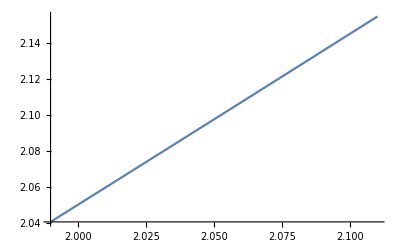

```mathematica
Plot[x+4/(20*x^2),{x,1.99,2.11}]
```